## RG for N = 2

We first  construct a stream plot for the differential equation (also called the beta function): (d g_i)/(d t) = g_i(ϵ - 1/2 ∑_(j=1)^N_c g_j^2 - g_i^2/N_c(1- 3/4 ∑_(j=1)^N_c g_j^2) +  3/(4 N_c)  ∑_(j=1)^N_c g_j^4)  when N = 2. Our results will  be studied only upto the power of ϵ^2 and 1/N_c. So, practically , we require N_c >> 1, while ϵ < 1.

```mathematica
RGlrgeNcN2g1[g1_, g2_,Nc_,e_]:= g1(e/2 -1/2(g1^2+g2^2)-g1^2/Nc (1-3/4(g1^2+g2^2))+ 3/(4Nc) (g1^4+g2^4) )
```

```mathematica
RGlrgeNcN2g2[g1_, g2_,Nc_,e_]:= g2(e/2 - 1/2(g1^2+g2^2)-g2^2/Nc (1-3/4(g1^2+g2^2))+ 3/(4Nc) (g1^4+g2^4) )
```

For the stream plot below, we set ϵ = 0.95, and N_c = 80

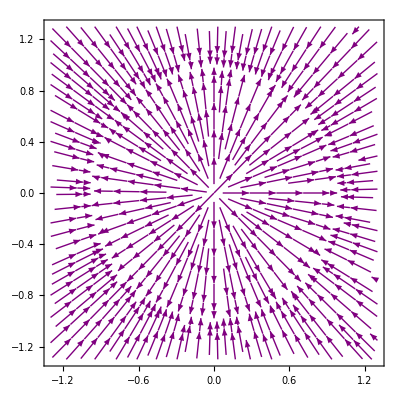

```mathematica
StreamPlot[{RGlrgeNcN2g1[g1, g2,Nc,0.95],RGlrgeNcN2g2[g1, g2,Nc,0.95]}/.{Nc->80},{g1,-1.3,1.3},{g2,-1.3,1.3},StreamScale->Automatic,StreamPoints->Fine,StreamColorFunction->None,StreamStyle->RGBColor[0.5,0,0.5]]
```

An interactive stream plot below where one can tune N_c between [4,20], and ϵ  between [1/2, 1]. 
Playing with the parameters, one can notice that when N_c is very large (ideally infinity), the fixed point solutions form a continuum manifold, approximately of the shape of a ring. On the other hand, on tuning down N_c, we find the manifold breaks up into 8 discrete fixed points. So, we are essentially observing a manifold breaking

```mathematica
Manipulate[StreamPlot[{RGlrgeNcN2g1[g1, g2,Nc,e],RGlrgeNcN2g2[g1, g2,Nc,e]},{g1,-1.3,1.3},{g2,-1.3,1.3},StreamScale->Automatic,StreamPoints->Fine],{Nc,4,20},{e,0.5,1}]
```

## Fixed point solutions for N = 2

### In polar coordinates

To solve for the fixed points (steady-state solutions), we re-writeg_1 = h cosϕ, g_2 = h sinϕ.   
The differential equation when ϕ = π/4, 3π/4, 5π/4, 7π/4, is,

```mathematica
lrgeNcplr1[h_,Nc_,e_]:= -e h+ h^2 + 1/Nc (h^2- (3 h^3)/2)
```

```mathematica
Solve[lrgeNcplr1[h,Nc,e]==0,h]
```

{{h→0},{h→1/3 (1+Nc-√(1+2 Nc-6 e Nc+Nc^2))},{h→1/3 (1+Nc+√(1+2 Nc-6 e Nc+Nc^2))}}

So,we find h = 1/3 (1 + N_c - √(1 + 2 N_c - 6 ϵ N_c + N_c^2)). Expanding in powers of ϵ and 1/N_c:

```mathematica
Normal[Series[1/3 (1+Nc-√(1+2 Nc-6 e Nc+Nc^2)),{e,0,2},{Nc,∞,1}]]
```

e (1-1/Nc)+(3 e^2)/(2 Nc)

When ϕ = 0, π/2, π, 3π/2, the RGE in terms of h becomes,

```mathematica
lrgeNcplr2[h_,Nc_,e_]:= -e h+ h^2 + 2/Nc (h^2- (3 h^3)/2)
```

```mathematica
Solve[lrgeNcplr2[h,Nc,e]==0,h]
```

{{h→0},{h→1/6 (2+Nc-√(4+4 Nc-12 e Nc+Nc^2))},{h→1/6 (2+Nc+√(4+4 Nc-12 e Nc+Nc^2))}}

So,we find h = 1/6 (2 + N_c - √(4 + 4 N_c - 12 ϵ N_c + N_c^2)). Expanding in powers of ϵ and 1/N_c:

```mathematica
Normal[Series[1/6 (2+Nc-√(4+4 Nc-12 e Nc+Nc^2)),{e,0,2},{Nc,∞,1}]]
```

e (1-2/Nc)+(3 e^2)/Nc

### Stability of fixed points

To understand the stability of fixed points, we linearize the beta functions around these point.To do that, First we take the first order partial derivatives w..rt each parameter, and then bring them together to end up at an eigenvalue problem as  dG/dt = M G, where G = (g_1, g_2), and M is a 2×2 matrix. 
 Here M is a function of g_1 and g_2. To find the stability of a fixed point, we plug in its (g_(1c), g_(2c)) to this matrix and calculate its eigenvalues.
  If the eigenvalues are all negative, the fixed point is stable. If all or some of them are positive, then the fixed point is not stable and must be fine-tuned. Number of positive eigenvalues give us a measure of stability (zero being most stable), while the corresponding eigenvectors tell the direction in which the system must be tuned.

```mathematica
dRGlrgeNcg1g1[g1_,g2_,Nc_,e_]:= D[RGlrgeNcN2g1[g1, g2,Nc,e],g1]
```

```mathematica
dRGlrgeNcg1g2[g1_,g2_,Nc_,e_]:= D[RGlrgeNcN2g1[g1, g2,Nc,e],g2]
```

```mathematica
dRGlrgeNcg2g1[g1_,g2_,Nc_,e_]:= D[RGlrgeNcN2g2[g1, g2,Nc,e],g1]
```

```mathematica
dRGlrgeNcg2g2[g1_,g2_,Nc_,e_]:= D[RGlrgeNcN2g2[g1, g2,Nc,e],g2]
```

```mathematica
lnrzbtamtrx[g1_,g2_,Nc_,e_]= {{dRGlrgeNcg1g1[g1,g2,Nc,e],dRGlrgeNcg1g2[g1,g2,Nc,e]},{dRGlrgeNcg2g1[g1,g2,Nc,e],dRGlrgeNcg2g2[g1,g2,Nc,e]}}
```

{{e/2+1/2 (-g1^2-g2^2)+g1 (-g1+(9 g1^3)/(2 Nc)-(2 g1 (1-3/4 (g1^2+g2^2)))/Nc)+(3 (g1^4+g2^4))/(4 Nc)-(g1^2 (1-3/4 (g1^2+g2^2)))/Nc,g1 (-g2+(3 g1^2 g2)/(2 Nc)+(3 g2^3)/Nc)},{g2 (-g1+(3 g1^3)/Nc+(3 g1 g2^2)/(2 Nc)),e/2+1/2 (-g1^2-g2^2)+g2 (-g2+(9 g2^3)/(2 Nc)-(2 g2 (1-3/4 (g1^2+g2^2)))/Nc)+(3 (g1^4+g2^4))/(4 Nc)-(g2^2 (1-3/4 (g1^2+g2^2)))/Nc}}

At ϕ = π/4, the fixed points are,

```mathematica
g1c[e_,Nc_]:= √(1/3 (1+Nc-√(1+2 Nc-6 e Nc+Nc^2))) Cos[π/4]
```

```mathematica
g2c[e_,Nc_]:=√(1/3 (1+Nc-√(1+2 Nc-6 e Nc+Nc^2))) Sin[π/4]
```

```mathematica
Normal[Simplify[Series[Eigenvalues[lnrzbtamtrx[g1c[e,Nc],g2c[e,Nc],Nc,e]],{e,0,2},{Nc,∞,1}],{e>0,Nc >0}]]
```

{-e+(3 e^2)/(2 Nc),-e/Nc+(3 e^2)/(4 Nc)}

Both eigenvalues are negative. Hence, the fixed point is stable. By symmetry, one can argue that it is the same case for all ϕ = π/4, 3π/4, 5π/4, 7π/4,.

At the point ϕ = π/2, the fixed point is:

```mathematica
g1c1[e_,Nc_]=√(1/6 (2+Nc-√(4+4 Nc-12 e Nc+Nc^2))) Cos[π/2]
```

0

```mathematica
g2c1[e_,Nc_]=√(1/6 (2+Nc-√(4+4 Nc-12 e Nc+Nc^2))) Sin[π/2]
```

(√(2+Nc-√(4+4 Nc-12 e Nc+Nc^2)))/(√6)

```mathematica
Normal[Series[Eigenvalues[lnrzbtamtrx[g1c1[e,Nc],g2c1[e,Nc],Nc,e]],{e,0,2},{Nc,∞,1}]]
```

{-e+(3 e^2)/Nc,e/Nc-(3 e^2)/(4 Nc)}

One eigenvalues is positive, and hence any perturbation along the corresponding eigenvector direction destabilizes the system and results in a flow.

```mathematica
Normal[Series[Eigensystem[lnrzbtamtrx[g1c1[e,Nc],g2c1[e,Nc],Nc,e]],{e,0,2},{Nc,∞,1}]   ]
```

{{-e+(3 e^2)/Nc,e/Nc-(3 e^2)/(4 Nc)},{{0,1},{1,0}}}

## Fixed points and their stability for N = 3.

As before, we re-write the parameters in terms of spherical coordinates as , g_1 = h sin θ cos ϕ, g_2 = h sin θ sin ϕ, g_3 = h cos θ  . RGE for the radial coordinates become:

```mathematica
f3[h_,θ_,ϕ_,e_,Nc_]:= -e/2 + 1/2 h+(1-1/2 Sin[2θ]^2-1/2 Sin[θ]^4 Sin[2ϕ]^2)(h/Nc  -3/2 h^2/Nc)
```

From symmetry, we could argue that there are three broad class of solutions. Below, we solve for the magnitude of ‘h’ in each case.

### when (g_(1c), g_(2c), g_(3c)) = g(1/(√3),1/(√3),1/(√3)) . Total 8 permutations

```mathematica
Simplify[Solve[{f3[h,ArcCos[1/(√3)],π/4,e,Nc]==0},h]]
```

{{h→1/6 (2+Nc (3+√((4+12 Nc-36 e Nc+9 Nc^2)/Nc^2)))},{h→1/6 (2-Nc (-3+√((4+12 Nc-36 e Nc+9 Nc^2)/Nc^2)))}}

```mathematica
Normal[Series[1/6 (2+Nc (3+√((4+12 Nc-36 e Nc+9 Nc^2)/Nc^2))),{Nc,∞,1},{e,0,2}]]
```

2/3-e+((2 e)/3-e^2)/Nc+Nc

```mathematica
Normal[Series[1/6 (2-Nc (-3+√((4+12 Nc-36 e Nc+9 Nc^2)/Nc^2))),{Nc,∞,1},{e,0,2}]]
```

e+(-(2 e)/3+e^2)/Nc

After series expansion, we find the latter one is the correct solution.

### when (g_(1c), g_(2c), g_(3c)) = g(1/(√2),1/(√2),0) . 12 permutations

```mathematica
Simplify[Solve[{f3[h,π/2,π/4,e,Nc]==0},h]]
```

{{h→1/3 (1+Nc-√(1+(2-6 e) Nc+Nc^2))},{h→1/3 (1+Nc+√(1+(2-6 e) Nc+Nc^2))}}

```mathematica
Normal[Series[1/3 (1+Nc-√(1+(2-6 e) Nc+Nc^2)),{Nc,∞,1},{e,0,2}]]
```

e+(-e+(3 e^2)/2)/Nc

### when (g_(1c), g_(2c), g_(3c)) = g(1,0,0) . 6 permutations

```mathematica
Simplify[Solve[{f3[h,0,0,e,Nc]==0},h]]
```

{{h→1/6 (2+Nc-√(4+(4-12 e) Nc+Nc^2))},{h→1/6 (2+Nc+√(4+(4-12 e) Nc+Nc^2))}}

```mathematica
Normal[Series[1/6 (2+Nc-√(4+(4-12 e) Nc+Nc^2)),{Nc,∞,1},{e,0,2}]]
```

e+(-2 e+3 e^2)/Nc

### IR stability

Now, we want to investigate the stability of these fixed point solutions. For this purpose, as before, we linearize the beta function around these fixed points. First we take the first order partial derivatives wrt each parameter, and then bring them together to end up at an eigenvalue problem as  dG/dt = M G, where G = (g_1, g_2, g_3), and M is a 3×3 matrix.

```mathematica
RGlrgeNcN3g1[g1_, g2_,g3_,Nc_,e_]:= g1(e/2 -1/2(g1^2+g2^2+g3^2)-g1^2/Nc (1-3/4(g1^2+g2^2+g3^2))+ 3/(4Nc) (g1^4+g2^4+g3^4) )
```

```mathematica
RGlrgeNcN3g2[g1_, g2_,g3_,Nc_,e_]:= g2(e/2 -1/2(g1^2+g2^2+g3^2)-g2^2/Nc (1-3/4(g1^2+g2^2+g3^2))+ 3/(4Nc) (g1^4+g2^4+g3^4) )
```

```mathematica
RGlrgeNcN3g3[g1_, g2_,g3_,Nc_,e_]:= g3(e/2 -1/2(g1^2+g2^2+g3^2)-g3^2/Nc (1-3/4(g1^2+g2^2+g3^2))+ 3/(4Nc) (g1^4+g2^4+g3^4) )
```

```mathematica
dRGlrgeNcN3g1g1[g1_, g2_,g3_,Nc_,e_]= D[RGlrgeNcN3g1[g1, g2,g3,Nc,e],g1]
```

e/2+1/2 (-g1^2-g2^2-g3^2)+g1 (-g1+(9 g1^3)/(2 Nc)-(2 g1 (1-3/4 (g1^2+g2^2+g3^2)))/Nc)+(3 (g1^4+g2^4+g3^4))/(4 Nc)-(g1^2 (1-3/4 (g1^2+g2^2+g3^2)))/Nc

```mathematica
dRGlrgeNcN3g1g2[g1_, g2_,g3_,Nc_,e_]= D[RGlrgeNcN3g1[g1, g2,g3,Nc,e],g2]
```

g1 (-g2+(3 g1^2 g2)/(2 Nc)+(3 g2^3)/Nc)

```mathematica
dRGlrgeNcN3g1g3[g1_, g2_,g3_,Nc_,e_]= D[RGlrgeNcN3g1[g1, g2,g3,Nc,e],g3]
```

g1 (-g3+(3 g1^2 g3)/(2 Nc)+(3 g3^3)/Nc)

```mathematica
dRGlrgeNcN3g2g1[g1_, g2_,g3_,Nc_,e_]= D[RGlrgeNcN3g2[g1, g2,g3,Nc,e],g1]
dRGlrgeNcN3g2g2[g1_, g2_,g3_,Nc_,e_]= D[RGlrgeNcN3g2[g1, g2,g3,Nc,e],g2]
dRGlrgeNcN3g2g3[g1_, g2_,g3_,Nc_,e_]= D[RGlrgeNcN3g2[g1, g2,g3,Nc,e],g3]
```

g2 (-g1+(3 g1^3)/Nc+(3 g1 g2^2)/(2 Nc))

e/2+1/2 (-g1^2-g2^2-g3^2)+g2 (-g2+(9 g2^3)/(2 Nc)-(2 g2 (1-3/4 (g1^2+g2^2+g3^2)))/Nc)+(3 (g1^4+g2^4+g3^4))/(4 Nc)-(g2^2 (1-3/4 (g1^2+g2^2+g3^2)))/Nc

g2 (-g3+(3 g2^2 g3)/(2 Nc)+(3 g3^3)/Nc)

```mathematica
dRGlrgeNcN3g3g1[g1_, g2_,g3_,Nc_,e_]= D[RGlrgeNcN3g3[g1, g2,g3,Nc,e],g1]
dRGlrgeNcN3g3g2[g1_, g2_,g3_,Nc_,e_]= D[RGlrgeNcN3g3[g1, g2,g3,Nc,e],g2]
dRGlrgeNcN3g3g3[g1_, g2_,g3_,Nc_,e_]= D[RGlrgeNcN3g3[g1, g2,g3,Nc,e],g3]
```

g3 (-g1+(3 g1^3)/Nc+(3 g1 g3^2)/(2 Nc))

g3 (-g2+(3 g2^3)/Nc+(3 g2 g3^2)/(2 Nc))

e/2+1/2 (-g1^2-g2^2-g3^2)+g3 (-g3+(9 g3^3)/(2 Nc)-(2 g3 (1-3/4 (g1^2+g2^2+g3^2)))/Nc)+(3 (g1^4+g2^4+g3^4))/(4 Nc)-(g3^2 (1-3/4 (g1^2+g2^2+g3^2)))/Nc

```mathematica
lnrzbtamtrxN3[g1_, g2_,g3_,Nc_,e_]= {{dRGlrgeNcN3g1g1[g1, g2,g3,Nc,e],dRGlrgeNcN3g1g2[g1, g2,g3,Nc,e],dRGlrgeNcN3g1g3[g1, g2,g3,Nc,e]},{dRGlrgeNcN3g2g1[g1, g2,g3,Nc,e],dRGlrgeNcN3g2g2[g1, g2,g3,Nc,e],dRGlrgeNcN3g2g3[g1, g2,g3,Nc,e]},{dRGlrgeNcN3g3g1[g1, g2,g3,Nc,e],dRGlrgeNcN3g3g2[g1, g2,g3,Nc,e],dRGlrgeNcN3g3g3[g1, g2,g3,Nc,e]}}
```

{{e/2+1/2 (-g1^2-g2^2-g3^2)+g1 (-g1+(9 g1^3)/(2 Nc)-(2 g1 (1-3/4 (g1^2+g2^2+g3^2)))/Nc)+(3 (g1^4+g2^4+g3^4))/(4 Nc)-(g1^2 (1-3/4 (g1^2+g2^2+g3^2)))/Nc,g1 (-g2+(3 g1^2 g2)/(2 Nc)+(3 g2^3)/Nc),g1 (-g3+(3 g1^2 g3)/(2 Nc)+(3 g3^3)/Nc)},{g2 (-g1+(3 g1^3)/Nc+(3 g1 g2^2)/(2 Nc)),e/2+1/2 (-g1^2-g2^2-g3^2)+g2 (-g2+(9 g2^3)/(2 Nc)-(2 g2 (1-3/4 (g1^2+g2^2+g3^2)))/Nc)+(3 (g1^4+g2^4+g3^4))/(4 Nc)-(g2^2 (1-3/4 (g1^2+g2^2+g3^2)))/Nc,g2 (-g3+(3 g2^2 g3)/(2 Nc)+(3 g3^3)/Nc)},{g3 (-g1+(3 g1^3)/Nc+(3 g1 g3^2)/(2 Nc)),g3 (-g2+(3 g2^3)/Nc+(3 g2 g3^2)/(2 Nc)),e/2+1/2 (-g1^2-g2^2-g3^2)+g3 (-g3+(9 g3^3)/(2 Nc)-(2 g3 (1-3/4 (g1^2+g2^2+g3^2)))/Nc)+(3 (g1^4+g2^4+g3^4))/(4 Nc)-(g3^2 (1-3/4 (g1^2+g2^2+g3^2)))/Nc}}

```mathematica
Series[Eigenvalues[lnrzbtamtrxN3[√(e/3-2/9 e/Nc+ 1/3 e^2/Nc), √(e/3-2/9 e/Nc+ 1/3 e^2/Nc),√(e/3-2/9 e/Nc+ 1/3 e^2/Nc),Nc,e]],{Nc,∞,1},{e,0,2}]
```

{(-(2 e)/3+e^2/2+O[e]^3)/Nc+O[1/Nc]^2,(-(2 e)/3+e^2/2+O[e]^3)/Nc+O[1/Nc]^2,(-e+O[e]^3)+(e^2+O[e]^3)/Nc+O[1/Nc]^2}

All the eigenvalues are negative. Hence the fixed point √(ϵ/3-2/9 ϵ/N_c+ 1/3 ϵ^2/N_c) (1,1,1) and its 8 permutations are stable.

```mathematica
Series[Eigenvalues[lnrzbtamtrxN3[√(e/2-1/2 e/Nc+ 3/4 e^2/Nc), √(e/2-1/2 e/Nc+ 3/4 e^2/Nc),0,Nc,e]],{Nc,∞,1},{e,0,2}]
```

{(-e+(3 e^2)/4+O[e]^3)/Nc+O[1/Nc]^2,(e/2-(3 e^2)/8+O[e]^3)/Nc+O[1/Nc]^2,(-e+O[e]^3)+((3 e^2)/2+O[e]^3)/Nc+O[1/Nc]^2}

One eigenvalue is positive while the other two are negative. Hence for the  fixed point √(ϵ/2-1/2 ϵ/N_c+ 3/4 ϵ^2/N_c) (1,1,0) and its 12 permutations, any perturbation along the unstable eigenvector direction will destabilize the system.

```mathematica
Series[Eigenvalues[lnrzbtamtrxN3[√(e -(2e)/Nc + (3 e^2)/Nc), 0,0,Nc,e]],{Nc,∞,1},{e,0,2}]
```

{(e-(3 e^2)/4+O[e]^3)/Nc+O[1/Nc]^2,(e-(3 e^2)/4+O[e]^3)/Nc+O[1/Nc]^2,(-e+O[e]^3)+(3 e^2+O[e]^3)/Nc+O[1/Nc]^2}

Two eigenvalues are positive while one is negative. Hence, the  fixed point √(ϵ-(2ϵ)/N_c+ (3 ϵ^2)/N_c) (1,0,0) and its 6 permutations are unstable everywhere except the one direction along the eigenvector of the negative eigenvalue. This eigenvector is normal to the 2D plane formed by the unstable eigenvectors